```mathematica
(* min z=4x1-3x2+5
 x1+4x2<=40
-2x1+2x2>=12
-3x1- x2<=15 *)
```

```mathematica
g1[x1_,x2_]:=x1+4x2;
g2[x1_,x2_]:=-2x1+2x2;
g3[x1_,x2_]:=-3x1-x2;
b1=40;
b2=12;
b3=15;
```

```mathematica
g1[x1_]=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]];
g3[x1_]=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]];
```

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-14,6},AspectRatio->1,PlotRange->{-5,15}]
```

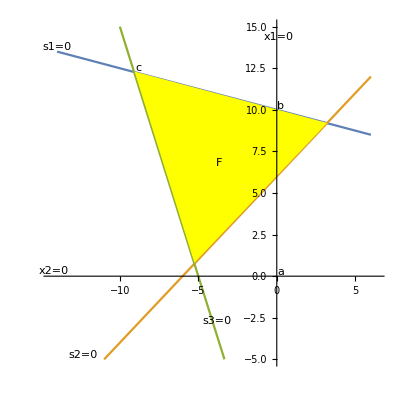

```mathematica
(* min z=4x1-3x2+5
 x1+4x2<=40
-2x1+2x2>=12
-3x1- x2<=15 *)
```

```mathematica
a0={"u1","u2","u3","u4",1,""};
a1={-1,1,-4,4,40,"s1"};
a2={-2,2,2,-2,-12,"s2"};
a3={3,-3,1,-1,15,"s3"};
aobj={4,-4,-3,3,5,"z"};
a={a0,a1,a2,a3,aobj};
Print["a = ",MatrixForm[a]]
```

a = (u1 | u2 | u3 | u4 | 1 | 
-1 | 1 | -4 | 4 | 40 | s1
-2 | 2 | 2 | -2 | -12 | s2
3 | -3 | 1 | -1 | 15 | s3
4 | -4 | -3 | 3 | 5 | z)

```mathematica
Dimensions[a]
Dimensions[a][[1]]
Dimensions[a][[2]]
```

{5,6}

5

6

```mathematica
pivot[iStar_,jStar_,tab_]:=(
nRows=Dimensions[tab][[1]];
nCols=Dimensions[tab][[2]];
newTab=tab;
newTab[[1,jStar]]=tab[[iStar,nCols]];
newTab[[iStar,nCols]]=tab[[1,jStar]];
For[ii=2,ii<=nRows,ii++,
For [jj=1,jj<nCols,jj++,
If[ii==iStar&&jj==jStar,newTab[[ii,jj]]=1/tab[[iStar,jStar]]](* p->1/p *);
If[ii==iStar&&jj!=jStar,newTab[[ii,jj]]=-tab[[ii,jj]]/tab[[iStar,jStar]]](* q->-q/p *);
If[ii!=iStar&&jj==jStar,newTab[[ii,jj]]=tab[[ii,jj]]/tab[[iStar,jStar]]](* r->r/p *);
If[ii!=iStar&&jj!=jStar,newTab[[ii,jj]]=tab[[ii,jj]]-tab[[iStar,jj]]tab[[ii,jStar]]/tab[[iStar,jStar]]](* s->s-(qr/p) *);
]
];
Return[newTab]
)
```

```mathematica
b=pivot[2,3,a];
Print["b = ",MatrixForm[b]]
```

b = (u1 | u2 | s1 | u4 | 1 | 
-1/4 | 1/4 | -1/4 | 1 | 10 | u3
-5/2 | 5/2 | -1/2 | 0 | 8 | s2
11/4 | -11/4 | -1/4 | 0 | 25 | s3
19/4 | -19/4 | 3/4 | 0 | -25 | z)

```mathematica
c=pivot[4,2,b];
Print["c = ",MatrixForm[c]]
```

c = (u1 | s3 | s1 | u4 | 1 | 
0 | -1/11 | -3/11 | 1 | 135/11 | u3
0 | -10/11 | -8/11 | 0 | 338/11 | s2
1 | -4/11 | -1/11 | 0 | 100/11 | u2
0 | 19/11 | 13/11 | 0 | -750/11 | z)